```mathematica
(*The eigenvalue is different between the BHPT and this papers definition*)
```

```mathematica
Genλms[lmax_,m_,γ_]:=Module[
{σ2 = -γ^2,M=m,Lmax=lmax,K,hold},
K=Table[σ2(1/3 KroneckerDelta[l,lc]+2/3 √((2l+1)/(2lc+1))Quiet[ClebschGordan[{l,m},{2,0},{lc,m}]ClebschGordan[{l,0},{2,0},{lc,0}]])+KroneckerDelta[l,lc]l(l+1),{lc,Abs[m],lmax},{l,Abs[m],lmax}];
Reverse[Eigenvalues[K]]
]
(*Output indexed by lc (Note shift lc->lc+1)*)
Genbms[lmax_,m_,γ_]:=Module[
{σ2 = -γ^2,M=m,Lmax=lmax,hold,K},
K=Table[σ2(1/3 KroneckerDelta[l,n]+2/3 √((2l+1)/(2n+1))Quiet[ClebschGordan[{l,m},{2,0},{n,m}]ClebschGordan[{l,0},{2,0},{n,0}]])+KroneckerDelta[l,n]l(l+1),{n,Abs[m],lmax},{l,Abs[m],lmax}];
hold = Reverse[Eigenvectors[K]];
hold
]
(*outputs Subscript[(b^l), l̂ m]=b[[l̂,l]]  (m is alrady fixed)*)

(*lmax-|m| gives the size of the matrix, lc is the highest l̂ required*)
GenAllb[lmax_,lcmax_,γ_]:=Module[
{Lmax=lmax,Lcmax = lcmax, g= γ},
Table[Genbms[Lmax,m,g],{m,-Lcmax,Lcmax}]
](*outputs Subscript[(b^l), l̂ m]=b[[m,l̂,l]], just remeber indexing starts at 1*)
```

```mathematica
(*b should be an output of GenAllb, and l̂ and m should obey the usual rule*)
Sdecomp[lc_,m_,γ_,θ_,b_]:=Sum[
Abs[b[[m+(Length[b]-1)/2+1,lc+1,l]]]SphericalHarmonicY[l-1,m,θ,0],{l,1,Length[b[[m+(Length[b]-1)/2+1,lc+1]]]}];
```

## Example:

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
M=1`32;
a = .9`32 M;
r0=10`32 M;
ω = 1/M 1/((r0/M)^(3/2)+a/M);
γ=a ω;
B =GenAllb[50,5,γ];
```

```mathematica
GG=Table[

If[Abs[m]≤lc,Show[Plot[Sdecomp[lc,m,γ,θ,B],{θ,0,π},PlotStyle->Black],
ListPlot[Table[{θ,SpinWeightedSpheroidalHarmonicS[0,lc,m,γ,θ,0,Method->"SphericalExpansion"]//Quiet},{θ,0,π,.1}],PlotStyle->Red],Ticks->None],Show[Graphics[{White,Circle[]}]]]
,{lc,0,5},{m,-5,5}];
```

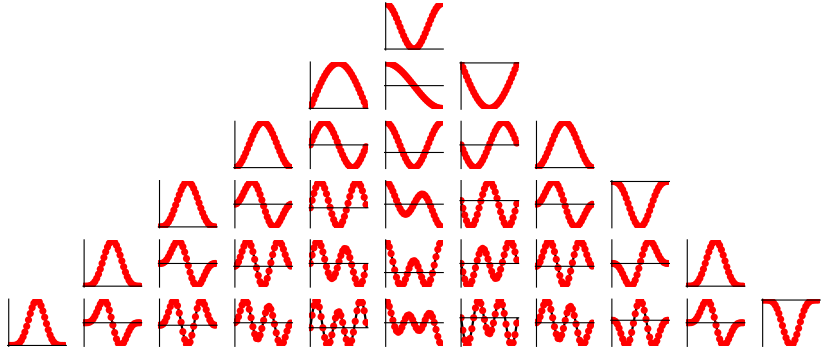

```mathematica
GraphicsGrid[GG]
```

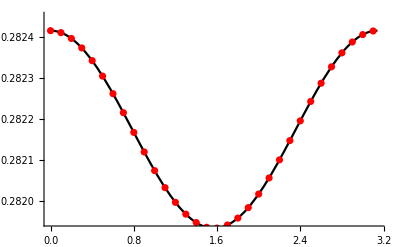

```mathematica
Show[
Plot[Sdecomp[0,0,γ,θ,B],{θ,0,π},PlotStyle->Black],
ListPlot[Table[{θ,SpinWeightedSpheroidalHarmonicS[0,0,0,γ,θ,0(*,Method->"SphericalExpansion"*)]},{θ,0,π,.1}],PlotStyle->Red],PlotRange->{{0,π},{.28195,.28245}}
]
```